```mathematica
Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];


headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
```

```mathematica
DFTC[list_,rev_]:=Module[{numItems,i,k,j,returnList,intensity},
returnList={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];
];

For[k=1,k<=numItems,k++,
intensity=list[[k]];
For [i=0,i<numItems/2,i++,
If[i==0 ||i==(numItems/2-1),
returnList[[i+1]]=returnList[[i+1]]+1/numItems*intensity*Cos[2*π *i *rev* (k-1)/numItems];,
returnList[[i+1]]=returnList[[i+1]]+2/numItems*intensity*Cos[2*π *i* rev *(k-1)/numItems];
];
];
];

returnList
];
DFTS[list_,rev_]:=Module[{numItems,i,k,j,reconstruction,returnList,errors,intensity},
returnList={};
errors={};
reconstruction={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnList,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnList[[k+1]]=returnList[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems];,
returnList[[k+1]]=returnList[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems];
];
];
];


For[j=0,j<numItems/2,j++,
AppendTo[errors,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstruction,0];
reconstruction[[i]]+=intensity;
For [k=0,k<numItems/2,k++,
reconstruction[[i]]-=returnList[k]*Sin[2*π*k*rev*(i-1)/numItems];
];
errors[[j]]+=Power[reconstruction[[i]]-returnList[[j]],2];
];
errors[[j]]=Sqrt[errors[[j]]/numItems];
];

{returnList,errors}
];
DFT[list_,rev_]:={DFTS[list,rev],DFTC[list,rev]};
```

```mathematica
folder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox","00School","Research","DataRuns","17-09-20"}];
folder=FileNameJoin[{"Z:","RbData","2017-09-22"}];
SetDirectory[folder];
FileNames[]
data=Import["lpDataCSV.csv","csv"];
data=Take[data,{1,-2},All];
angle=Transpose[data][[1]];
intensityArray=Transpose[data][[2]];
angleRAD=angle*π/180;

fc=DFT[intensityArray,1] (*fc=fourier coefficients*)
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
```

{FDayRotation2017-09-22_101927.dat,FDayRotation2017-09-22_101927.png,FDayRotation2017-09-22_101927RotationAnalysis.dat,FDayRotation2017-09-22_101951.dat,FDayRotation2017-09-22_101951.png,FDayRotation2017-09-22_101951RotationAnalysis.dat,FDayRotation2017-09-22_102015.dat,FDayRotation2017-09-22_102015.png,FDayRotation2017-09-22_102015RotationAnalysis.dat,FDayRotation2017-09-22_102039.dat,FDayRotation2017-09-22_102039.png,FDayRotation2017-09-22_102039RotationAnalysis.dat,FDayRotation2017-09-22_102103.dat,FDayRotation2017-09-22_102103.png,FDayRotation2017-09-22_102103RotationAnalysis.dat,FDayRotation2017-09-22_102127.dat,FDayRotation2017-09-22_102127.png,FDayRotation2017-09-22_102127RotationAnalysis.dat,FDayRotation2017-09-22_102151.dat,FDayRotation2017-09-22_102151.png,FDayRotation2017-09-22_102151RotationAnalysis.dat,FDayRotation2017-09-22_102214.dat,FDayRotation2017-09-22_102214.png,FDayRotation2017-09-22_102214RotationAnalysis.dat,FDayRotation2017-09-22_102238.dat,FDayRotation2017-09-22_102238.png,FDayRotation2017-09-22_102238RotationAnalysis.dat,FDayRotation2017-09-22_102302.dat,FDayRotation2017-09-22_102302.png,FDayRotation2017-09-22_102302RotationAnalysis.dat,FDayRotation2017-09-22_121024.dat,FDayRotation2017-09-22_121024.png,FDayRotation2017-09-22_121024RotationAnalysis.dat,FDayRotation2017-09-22_121051.dat,FDayRotation2017-09-22_121232.dat,FDayRotation2017-09-22_121232.png,FDayRotation2017-09-22_121232RotationAnalysis.dat,FDayRotation2017-09-22_121302.dat,FDayRotation2017-09-22_121302.png,FDayRotation2017-09-22_121302RotationAnalysis.dat,FDayRotation2017-09-22_121328.dat,FDayRotation2017-09-22_121328.png,FDayRotation2017-09-22_121328RotationAnalysis.dat,FDayRotation2017-09-22_121355.dat,FDayRotation2017-09-22_121355.png,FDayRotation2017-09-22_121355RotationAnalysis.dat,FDayRotation2017-09-22_121421.dat,FDayRotation2017-09-22_121421.png,FDayRotation2017-09-22_121421RotationAnalysis.dat,FDayRotation2017-09-22_121448.dat,FDayRotation2017-09-22_121448.png,FDayRotation2017-09-22_121448RotationAnalysis.dat,FDayRotation2017-09-22_121514.dat,FDayRotation2017-09-22_121514.png,FDayRotation2017-09-22_121514RotationAnalysis.dat,FDayRotation2017-09-22_121541.dat,FDayRotation2017-09-22_121541.png,FDayRotation2017-09-22_121541RotationAnalysis.dat,FDayRotation2017-09-22_121607.dat,FDayRotation2017-09-22_121607.png,FDayRotation2017-09-22_121607RotationAnalysis.dat,FDayRotation2017-09-22_121633.dat,FDayRotation2017-09-22_121633.png,FDayRotation2017-09-22_121633RotationAnalysis.dat,FDayRotation2017-09-22_123902.dat,FDayRotation2017-09-22_123902.png,FDayRotation2017-09-22_123902RotationAnalysis.dat,FDayRotation2017-09-22_123926.dat,FDayRotation2017-09-22_123926.png,FDayRotation2017-09-22_123926RotationAnalysis.dat,FDayRotation2017-09-22_123949.dat,FDayRotation2017-09-22_123949.png,FDayRotation2017-09-22_123949RotationAnalysis.dat,FDayRotation2017-09-22_124013.dat,FDayRotation2017-09-22_124013.png,FDayRotation2017-09-22_124013RotationAnalysis.dat,FDayRotation2017-09-22_124037.dat,FDayRotation2017-09-22_124037.png,FDayRotation2017-09-22_124037RotationAnalysis.dat,FDayRotation2017-09-22_124408.dat,FDayRotation2017-09-22_124408.png,FDayRotation2017-09-22_124408RotationAnalysis.dat,FDayRotation2017-09-22_124432.dat,FDayRotation2017-09-22_124432.png,FDayRotation2017-09-22_124432RotationAnalysis.dat,FDayRotation2017-09-22_124456.dat,FDayRotation2017-09-22_124456.png,FDayRotation2017-09-22_124456RotationAnalysis.dat,FDayRotation2017-09-22_124520.dat,FDayRotation2017-09-22_124520.png,FDayRotation2017-09-22_124520RotationAnalysis.dat,FDayRotation2017-09-22_124544.dat,FDayRotation2017-09-22_124544.png,FDayRotation2017-09-22_124544RotationAnalysis.dat,FDayRotation2017-09-22_124824.dat,FDayRotation2017-09-22_124824.png,FDayRotation2017-09-22_124824RotationAnalysis.dat,FDayRotation2017-09-22_124849.dat,FDayRotation2017-09-22_124849.png,FDayRotation2017-09-22_124849RotationAnalysis.dat,FDayRotation2017-09-22_124913.dat,FDayRotation2017-09-22_124913.png,FDayRotation2017-09-22_124913RotationAnalysis.dat,FDayRotation2017-09-22_124937.dat,FDayRotation2017-09-22_124937.png,FDayRotation2017-09-22_124937RotationAnalysis.dat,FDayRotation2017-09-22_125001.dat,FDayRotation2017-09-22_125001.png,FDayRotation2017-09-22_125001RotationAnalysis.dat,FDayRotation2017-09-22_125313.dat,FDayRotation2017-09-22_125313.png,FDayRotation2017-09-22_125313RotationAnalysis.dat,FDayRotation2017-09-22_125337.dat,FDayRotation2017-09-22_125337.png,FDayRotation2017-09-22_125337RotationAnalysis.dat,FDayRotation2017-09-22_125401.dat,FDayRotation2017-09-22_125401.png,FDayRotation2017-09-22_125401RotationAnalysis.dat,FDayRotation2017-09-22_125425.dat,FDayRotation2017-09-22_125425.png,FDayRotation2017-09-22_125425RotationAnalysis.dat,FDayRotation2017-09-22_125448.dat,FDayRotation2017-09-22_125448.png,FDayRotation2017-09-22_125448RotationAnalysis.dat,FDayRotation2017-09-22_125741.dat,FDayRotation2017-09-22_125741.png,FDayRotation2017-09-22_125741RotationAnalysis.dat,FDayRotation2017-09-22_125804.dat,FDayRotation2017-09-22_125804.png,FDayRotation2017-09-22_125804RotationAnalysis.dat,FDayRotation2017-09-22_125828.dat,FDayRotation2017-09-22_125828.png,FDayRotation2017-09-22_125828RotationAnalysis.dat,FDayRotation2017-09-22_125852.dat,FDayRotation2017-09-22_125852.png,FDayRotation2017-09-22_125852RotationAnalysis.dat,FDayRotation2017-09-22_125916.dat,FDayRotation2017-09-22_125916.png,FDayRotation2017-09-22_125916RotationAnalysis.dat,FDayRotation2017-09-22_132036.dat,FDayRotation2017-09-22_132036.png,FDayRotation2017-09-22_132036RotationAnalysis.dat,FDayRotation2017-09-22_132100.dat,FDayRotation2017-09-22_132100.png,FDayRotation2017-09-22_132100RotationAnalysis.dat,FDayRotation2017-09-22_132124.dat,FDayRotation2017-09-22_132124.png,FDayRotation2017-09-22_132124RotationAnalysis.dat,FDayRotation2017-09-22_132148.dat,FDayRotation2017-09-22_132148.png,FDayRotation2017-09-22_132148RotationAnalysis.dat,FDayRotation2017-09-22_132212.dat,FDayRotation2017-09-22_132212.png,FDayRotation2017-09-22_132212RotationAnalysis.dat,FDayRotation2017-09-22_132626.dat,FDayRotation2017-09-22_132626.png,FDayRotation2017-09-22_132626RotationAnalysis.dat,FDayRotation2017-09-22_132651.dat,FDayRotation2017-09-22_132651.png,FDayRotation2017-09-22_132651RotationAnalysis.dat,FDayRotation2017-09-22_132715.dat,FDayRotation2017-09-22_132715.png,FDayRotation2017-09-22_132715RotationAnalysis.dat,FDayRotation2017-09-22_132739.dat,FDayRotation2017-09-22_132739.png,FDayRotation2017-09-22_132739RotationAnalysis.dat,FDayRotation2017-09-22_132803.dat,FDayRotation2017-09-22_132803.png,FDayRotation2017-09-22_132803RotationAnalysis.dat,FDayRotation2017-09-22_133050.dat,FDayRotation2017-09-22_133050.png,FDayRotation2017-09-22_133050RotationAnalysis.dat,FDayRotation2017-09-22_133114.dat,FDayRotation2017-09-22_133114.png,FDayRotation2017-09-22_133114RotationAnalysis.dat,FDayRotation2017-09-22_133138.dat,FDayRotation2017-09-22_133138.png,FDayRotation2017-09-22_133138RotationAnalysis.dat,FDayRotation2017-09-22_133202.dat,FDayRotation2017-09-22_133202.png,FDayRotation2017-09-22_133202RotationAnalysis.dat,FDayRotation2017-09-22_133225.dat,FDayRotation2017-09-22_133225.png,FDayRotation2017-09-22_133225RotationAnalysis.dat,FDayRotation2017-09-22_133757.dat,FDayRotation2017-09-22_133757.png,FDayRotation2017-09-22_133757RotationAnalysis.dat,FDayRotation2017-09-22_133821.dat,FDayRotation2017-09-22_133821.png,FDayRotation2017-09-22_133821RotationAnalysis.dat,FDayRotation2017-09-22_133845.dat,FDayRotation2017-09-22_133845.png,FDayRotation2017-09-22_133845RotationAnalysis.dat,FDayRotation2017-09-22_133909.dat,FDayRotation2017-09-22_133909.png,FDayRotation2017-09-22_133909RotationAnalysis.dat,FDayRotation2017-09-22_133933.dat,FDayRotation2017-09-22_133933.png,FDayRotation2017-09-22_133933RotationAnalysis.dat,FDayRotation2017-09-22_134151.dat,FDayRotation2017-09-22_134151.png,FDayRotation2017-09-22_134151RotationAnalysis.dat,FDayRotation2017-09-22_134215.dat,FDayRotation2017-09-22_134215.png,FDayRotation2017-09-22_134215RotationAnalysis.dat,FDayRotation2017-09-22_134239.dat,FDayRotation2017-09-22_134239.png,FDayRotation2017-09-22_134239RotationAnalysis.dat,FDayRotation2017-09-22_134303.dat,FDayRotation2017-09-22_134303.png,FDayRotation2017-09-22_134303RotationAnalysis.dat,FDayRotation2017-09-22_134327.dat,FDayRotation2017-09-22_134327.png,FDayRotation2017-09-22_134327RotationAnalysis.dat,FDayRotation2017-09-22.dat}

Import::nffil: File not found during Import.

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,{1,-2},All].

Part::partw: Part 2 of Transpose[Take[$Failed,{1,-2},All]] does not exist.

{{0},{1+1/2 Transpose[Take[$Failed,{1,-2},All]]}}

Part::partw: Part 3 of {1+1/2 Transpose[Take[$Failed,{1,-2},All]]} does not exist.

Part::partw: Part 3 of {0} does not exist.

(√(({0}⟦3⟧)^2+({1+1/2 Transpose[Take[$Failed,{1,-2},All]]}⟦3⟧)^2))/(1+1/2 Transpose[Take[$Failed,{1,-2},All]])

```mathematica
folder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox","00School","Research","DataRuns","17-09-20"}];
```

```mathematica
GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];
```

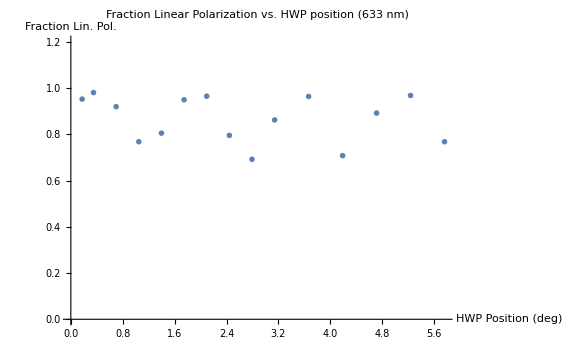

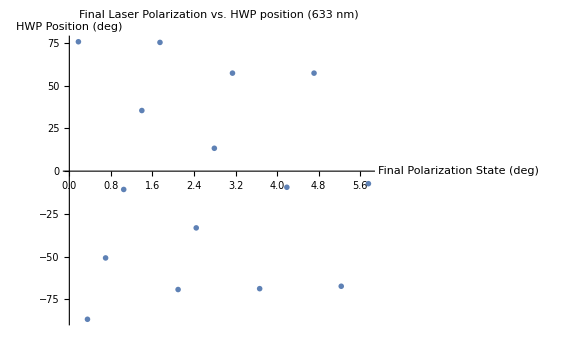

```mathematica
hwpAngles={10,20,40,60,80,100,120,140,160,180,210,240,270,300,330};
hwpAngles=hwpAngles*π/180;
percentPol={.9520,.9802,.9193,.7678,.8048,.9489,.9646,.7951,.6917,.8619,.9635,.7075,.8916,.9676,.7677};
laserPolarizationAngle={75.65,-86.60,-50.74,-10.71,35.44,75.26,-69.21,-33.17,13.37,57.30,-68.70,-9.42,57.30,-67.29,-7.32};
plotTitle="Fraction Linear Polarization vs. HWP position (633 nm)";
xAxisTitle="Fraction Lin. Pol.";
yAxisTitle="HWP Position (deg)";
plot633=ListPlot[Transpose[{hwpAngles,percentPol}],PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotRange->{0,1.2},PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}]

plotTitle="Final Laser Polarization vs. HWP position (633 nm)";
yAxisTitle="Final Polarization State (deg)";
xAxisTitle="HWP Position (deg)";
ListPlot[Transpose[{hwpAngles,laserPolarizationAngle}],PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}]
```

## Determing Fraction of LP without the HWP in.

{0.997291,0.998362,0.996816,0.996694,0.995883,0.998316,0.996829,0.997882,0.996804,0.998814}

{32.0451,32.0534,32.0539,32.0162,32.0866,32.1441,31.9737,32.0412,32.0517,32.0411}

{0.997369,0.000931965}

{32.0507,0.0439114}

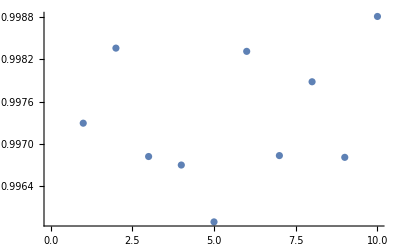

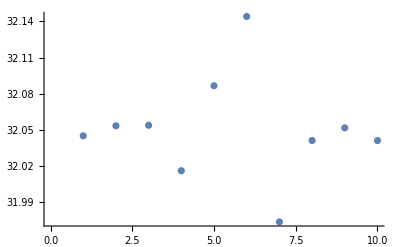

```mathematica
times={101927,101951,102015,102039,102103,102127,102151,102214,102238,102302};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
{Mean[fractions],StandardDeviation[fractions]}
{Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
```

## Increasing motor delay to 5 ms

{121232,121302,121328,121355,121421,121448,121514,121541,121607,121633}

{0.993895,0.999145,0.996628,1.00013,0.996001,0.999871,0.997476,0.998485,0.996484,0.998307}

{32.0171,32.034,32.0559,31.9752,32.0781,32.1003,32.1357,32.0703,32.0609,32.0655}

{0.997642,0.00193431}

{32.0593,0.0441424}

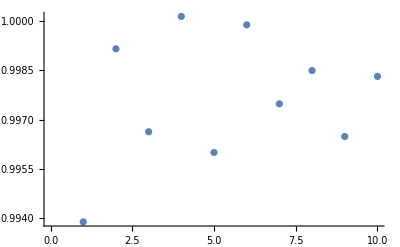

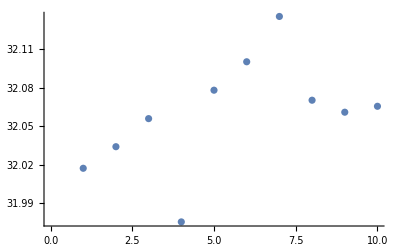

```mathematica
times={121232,121302,121328,121355,121421,121448,121514,121541,121607,121633}
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
{Mean[fractions],StandardDeviation[fractions]}
{Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
```

### Decreasing motor delay to 2.5 ms, as it didn’t seem to make a difference. HWP is now in and at 0 degrees. Stepping through in 20 degree increments.

```mathematica
hwpAngles=Range[0,360,20];
hwpResults=hwpAngles
```

{0,20,40,60,80,100,120,140,160,180,200,220,240,260,280,300,320,340,360}

#### HWP=0

{123902,123926,123949,124013,124037}

{0.117769,0.117214,0.116313,0.118792,0.118036}

{89.8255,89.5994,89.8399,89.4796,89.8961}

{0.117625,0.000927877}

{89.7281,0.179263}

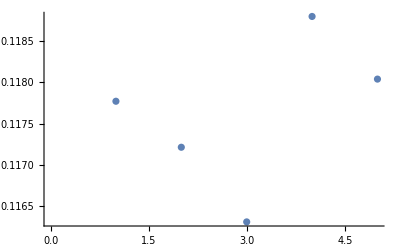

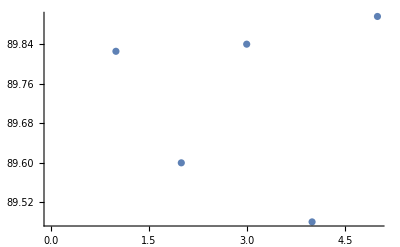

```mathematica
times={123902,123926,123949,124013,124037}
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[1]]={hwpAngles[[1]],polFraction,laserAngle};
```

#### HWP=20

{124408,124432,124456,124520,124544}

{0.561126,0.560293,0.55734,0.559659,0.561003}

{0.371483,0.378377,0.257209,0.126633,0.39299}

{0.559884,0.00153988}

{0.305339,0.113627}

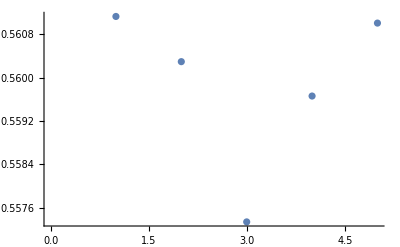

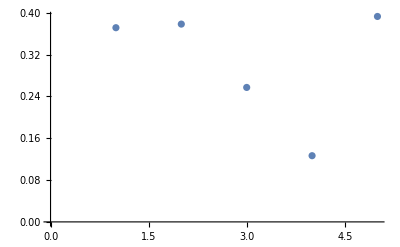

```mathematica
times={124408,124432,124456,124520,124544}
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[2]]={hwpAngles[[2]],polFraction,laserAngle};
```

#### HWP=40

{24.0238,24.0191,24.1169,24.054,24.0129}

{0.954096,0.00167881}

{24.0453,0.0429996}

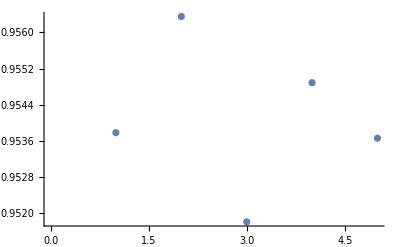

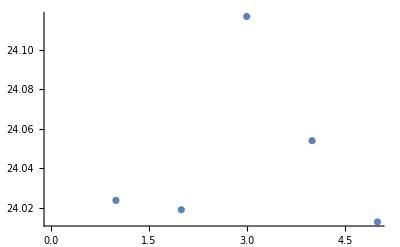

```mathematica
times={124824,124849,124913,124937,125001};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[3]]={hwpAngles[[3]],polFraction,laserAngle};
```

#### HWP=60

{0.914525,0.915684,0.912582,0.913423,0.915036}

{45.7607,45.9271,45.6936,45.8244,45.7357}

{0.91425,0.00124659}

{45.7883,0.0909161}

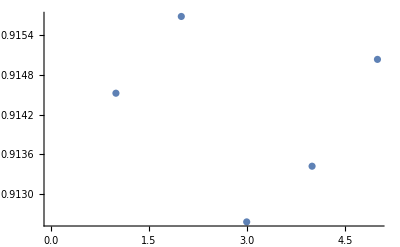

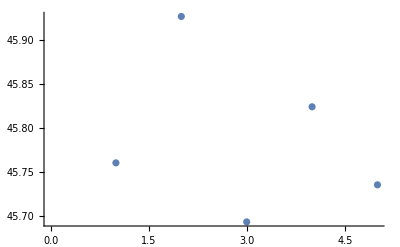

```mathematica
times={125313,125337,125401,125425,125448};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[4]]={hwpAngles[[4]],polFraction,laserAngle};
```

#### HWP = 80

{0.428582,0.430911,0.42928,0.430998,0.427847}

{70.9689,71.0549,71.094,71.1311,71.0526}

{0.429523,0.00140155}

{71.0603,0.0603946}

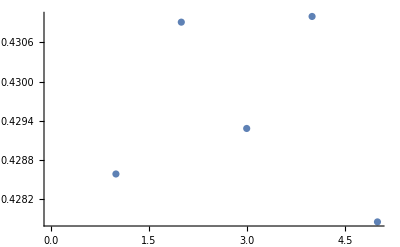

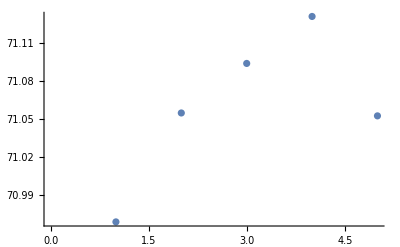

```mathematica
times={125741,125804,125828,125852,125916};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[5]]={hwpAngles[[5]],polFraction,laserAngle};
```

#### HWP = 100

{0.266606,0.271295,0.267216,0.268309,0.270276}

{-19.4409,-19.3269,-19.2605,-19.369,-19.2328}

{0.26874,0.00199662}

{-19.326,0.0837018}

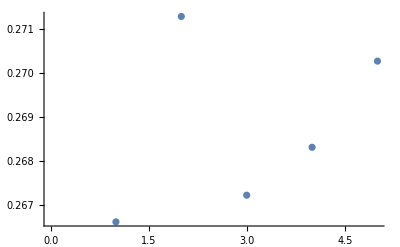

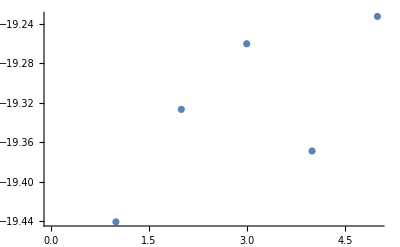

```mathematica
times={132036,132100,132124,132148,132212};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[6]]={hwpAngles[[6]],polFraction,laserAngle};
```

#### HWP = 120

{0.778338,0.781365,0.78146,0.780442,0.780903}

{11.2568,11.1569,11.1808,11.2376,11.188}

{0.780502,0.00127557}

{11.204,0.041633}

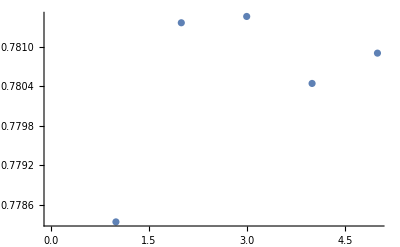

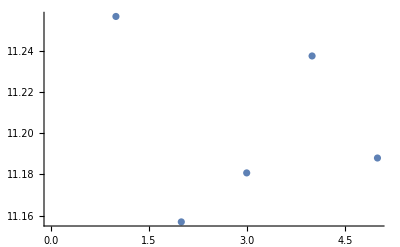

```mathematica
times={132626,132651,132715,132739,132803};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[7]]={hwpAngles[[7]],polFraction,laserAngle};
```

#### HWP = 140

{1.0009,0.997439,0.998875,0.996983,1.00011}

{33.2202,33.1506,33.1781,33.1609,33.173}

{0.99886,0.00167695}

{33.1765,0.0266393}

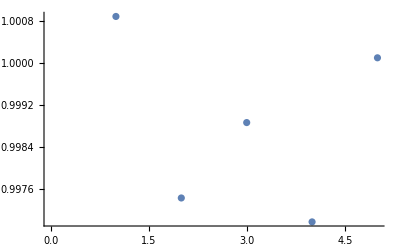

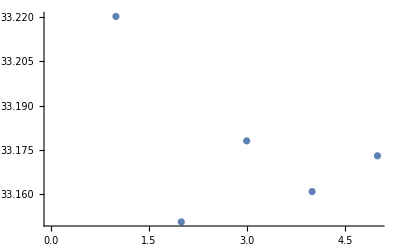

```mathematica
times={133050,133114,133138,133202,133225};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[8]]={hwpAngles[[8]],polFraction,laserAngle};
```

#### On the previous run, I note the high linear polarization and the closeness, to the angle measured without the HWP in.

#### HWP = 160

{0.726323,0.728362,0.725786,0.726653,0.729184}

{54.4768,54.4603,54.512,54.3472,54.4857}

{0.727262,0.00144362}

{54.4564,0.0638721}

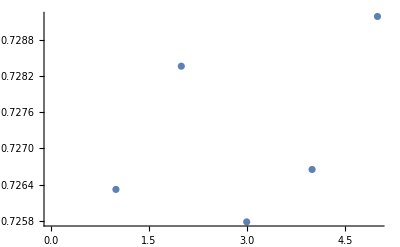

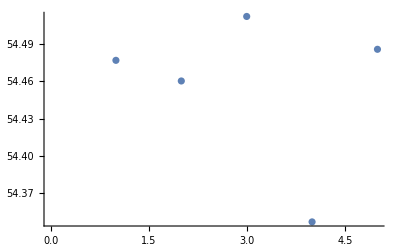

```mathematica
times={133757,133821,133845,133909,133933};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[9]]={hwpAngles[[9]],polFraction,laserAngle};
```

#### HWP = 180

{0.126038,0.122972,0.124888,0.122073,0.12316}

{-84.1457,-84.4907,-83.8436,-83.7251,-84.2006}

{0.123826,0.00160194}

{-84.0812,0.303871}

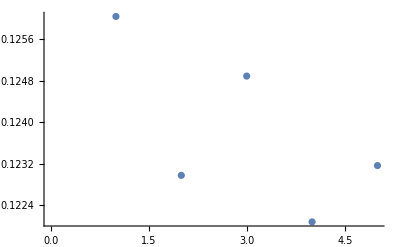

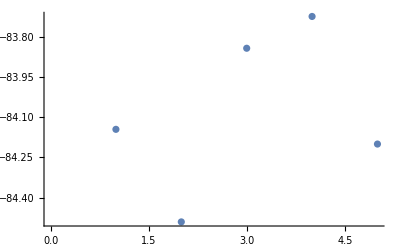

```mathematica
times={134151,134215,134239,134303,134327};
names=GenerateListOfFileNames["FDayRotation","2017-09-22",times];
fractions=GetLinearPolarizationFraction[names]
angles=GetAngle[names]*180/π
polFraction={Mean[fractions],StandardDeviation[fractions]}
laserAngle={Mean[angles],StandardDeviation[angles]}
ListPlot[fractions]
ListPlot[angles]
hwpResults[[10]]={hwpAngles[[10]],polFraction,laserAngle};
```

```mathematica
hwpResults=Take[hwpResults,{1,10}]
```

{{0,{0.117625,0.000927877},{89.7281,0.179263}},{20,{0.559884,0.00153988},{0.305339,0.113627}},{40,{0.954096,0.00167881},{24.0453,0.0429996}},{60,{0.91425,0.00124659},{45.7883,0.0909161}},{80,{0.429523,0.00140155},{71.0603,0.0603946}},{100,{0.26874,0.00199662},{-19.326,0.0837018}},{120,{0.780502,0.00127557},{11.204,0.041633}},{140,{0.99886,0.00167695},{33.1765,0.0266393}},{160,{0.727262,0.00144362},{54.4564,0.0638721}},{180,{0.123826,0.00160194},{-84.0812,0.303871}}}

```mathematica
Transpose[hwpResults]
```

{{0,20,40,60,80,100,120,140,160,180},{{0.117625,0.000927877},{0.559884,0.00153988},{0.954096,0.00167881},{0.91425,0.00124659},{0.429523,0.00140155},{0.26874,0.00199662},{0.780502,0.00127557},{0.99886,0.00167695},{0.727262,0.00144362},{0.123826,0.00160194}},{{89.7281,0.179263},{0.305339,0.113627},{24.0453,0.0429996},{45.7883,0.0909161},{71.0603,0.0603946},{-19.326,0.0837018},{11.204,0.041633},{33.1765,0.0266393},{54.4564,0.0638721},{-84.0812,0.303871}}}

```mathematica
newList={};
Length[hwpResults]
For[j=1,j≤Length[hwpResults],j++,
AppendTo[newList,{{hwpResults[[j]][[1]]*π/180,hwpResults[[j]][[2]][[1]]},ErrorBar[hwpResults[[j]][[2]][[2]]]}];
];
newList2={};
For[j=1,j≤Length[hwpResults],j++,
AppendTo[newList2,{{hwpResults[[j]][[1]]*π/180,hwpResults[[j]][[3]][[1]]},ErrorBar[hwpResults[[j]][[3]][[2]]]}];
];
plotTitle="Fraction Linear Polarization vs. HWP position (795 nm)";
xAxisTitle="Fraction of Linear Polarization";
yAxisTitle="HWP Position (deg)";
plot795=ErrorListPlot[newList,PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotRange->{0,1},PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}]
plotTitle="Final Laser Polarization vs. HWP position (795 nm)";
yAxisTitle="Final Polarization State (deg)";
xAxisTitle="HWP Position (deg)";
plottingOptions={PlotMarkers->{Automatic,Medium},LabelStyle->18,ImageSize->Large,PlotLabel-> plotTitle,AxesLabel->{yAxisTitle,xAxisTitle}};
ErrorListPlot[newList2,Evaluate[plottingOptions]]
```

0

ErrorListPlot[{},PlotMarkers→{Automatic,Medium},LabelStyle→18,ImageSize→Large,PlotRange→{0,1},PlotLabel→Fraction Linear Polarization vs. HWP position (795 nm),AxesLabel→{HWP Position (deg),Fraction of Linear Polarization}]

ErrorListPlot[{},{PlotMarkers→{Automatic,Medium},LabelStyle→18,ImageSize→Large,PlotLabel→Final Laser Polarization vs. HWP position (795 nm),AxesLabel→{Final Polarization State (deg),HWP Position (deg)}}]

```mathematica
retardance633=780^2/(2 633);
N[retardance633/633]

retardance795=780^2/(2 795);
N[retardance795/795]
```

0.759192

0.48131

#### According to a Chp 22 in an optics handbook (chapter authored by Russell A. Chipman), We have the following mueller matrix for a general retarder

```mathematica
LR[θfast_,retardance_]:=({{1, 0, 0, 0}, {0, Cos[2θfast]^2+Sin[2θfast]^2Cos[2π retardance], Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), -Sin[2θfast]Sin[2π retardance]}, {0, Sin[2θfast]Cos[2θfast](1-Cos[2π retardance]), Sin[2θfast]^2+Cos[2θfast]Cos[2π retardance]^2, Cos[2 θfast]Sin[2π retardance]}, {0, Sin[2θfast]Sin[2π retardance], -Cos[2 θfast]Sin[2π retardance], Cos[2π retardance]}})
LRzero[δ_]:=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[δ], Sin[δ]}, {0, 0, -Sin[δ], Cos[δ]}});
LPzero=1/2({{1, 1, 0, 0}, {1, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

#### We will assume our incident vector was 100% linearly polarized in the horizontal direction

```mathematica
inc=({{1}, {1}, {0}, {0}})
MatrixForm[(MuellerRotation[θ].LRzero[δ].Transpose[MuellerRotation[θ]])]
```

{{1},{1},{0},{0}}

MuellerRotation[θ].{{1,0,0,0},{0,1,0,0},{0,0,{0.569006,0.886579,0.890933,0.999685},{0.822334,0.462577,0.454134,0.0250974}},{0,0,{-0.822334,-0.462577,-0.454134,-0.0250974},{0.569006,0.886579,0.890933,0.999685}}}.Transpose[MuellerRotation[θ]]

#### A useful tool is the rotation matrix

```mathematica
MuellerRotation[θ_]:=({{1, 0, 0, 0}, {0, Cos[2θ], -Sin[2θ], 0}, {0, Sin[2θ], Cos[2θ], 0}, {0, 0, 0, 1}})
newLP=LPzero
```

{{1/2,1/2,0,0},{1/2,1/2,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Clear[newLR]
newLR[θ_,δ_]:=(MuellerRotation[θ].LRzero[δ].Transpose[MuellerRotation[θ]])
```

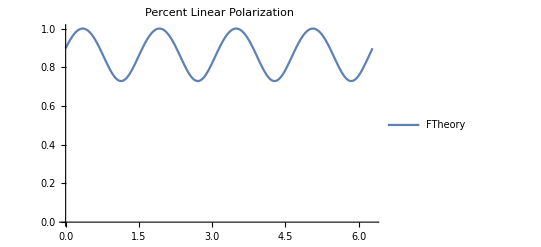

```mathematica
retardance=3.38;
shift795=42*π/180;
shift633=-20*π/180;
shift=shift633;
theory=Plot[Legended[Sqrt[(((LR[θ+shift,retardance].newLP.inc)[[2]])^2+((LR[θ+shift,retardance].newLP.inc)[[3]])^2)]/(LR[θ+shift,retardance].newLP.inc)[[1]],"FTheory"],{θ,0,2π},PlotRange->{0,Automatic},PlotLabel->"Percent Linear Polarization"]
```

```mathematica
Rasterize[Show[plot795,theory]]
```

-Graphics-

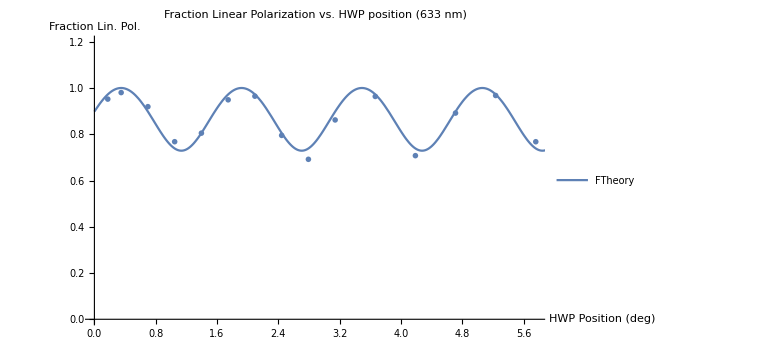

-Graphics-

```mathematica
Show[plot633,theory]
Rasterize[%]
```

1.5708

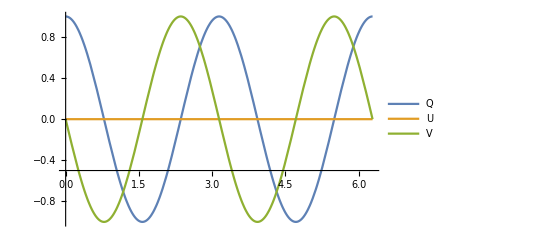

3.14159

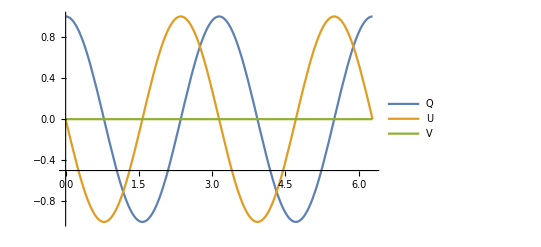

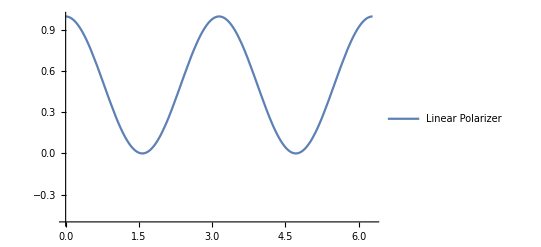

```mathematica
retard=.25*2*π
Plot[{Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[2]],"Q"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[3]],"U"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[4]],"V"]},{θ,0,2π},AxesOrigin->{0,-.5}]
retard=.5*2*π
Plot[{Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[2]],"Q"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[3]],"U"],Legended[(newLR[0,retard].MuellerRotation[θ].inc)[[4]],"V"]},{θ,0,2π},AxesOrigin->{0,-.5}]
Plot[Legended[(LPzero.MuellerRotation[θ].inc)[[2]],"Linear Polarizer"],{θ,0,2π},AxesOrigin->{0,-.5}]
```